```mathematica
H[x_,y_]=Sin[x](1+b Cos[y]);
Hx[x_,y_]=Cos[x](1+b Cos[y]);
Hy[x_,y_]=-b Sin[x]Sin[y];
```

```mathematica
(* existence function *)
Γ=v/Integrate[Exp[-s]H[v s,0],{s,0,Infinity},Assumptions->{v∈Reals}]
```

(1+v^2)/(1+b)

```mathematica
(* stability functions *)
d1=Integrate[Exp[-s]Hx[v s,0](Exp[-(x+y I)s]-1),{s,0,Infinity},Assumptions->{v∈Reals,x∈Reals,y∈Reals,x>-1,y>-1}];
d2=Integrate[Exp[-s]Hx[0,v s](Exp[-(x+y I)s]-1),{s,0,Infinity},Assumptions->{v∈Reals,x∈Reals,y∈Reals,x>-1,y>-1}];
```

```mathematica
d1re=FullSimplify[ComplexExpand[Re[d1]]];
d1im=FullSimplify[ComplexExpand[Im[d1]]];
```

```mathematica
L1re=x+Γ d1re/.b->.8/.v->.4;
L1im=y+Γ d1im/.b->.8/.v->.4;
```

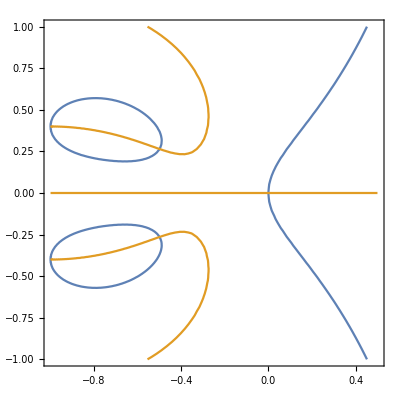

```mathematica
ContourPlot[{L1re==0,L1im==0},{x,-1,.5},{y,-1,1},PlotPoints->20]
```

```mathematica
FullSimplify[(λ+v/Γ d1)/λ==0]
```

(2. v^2+λ (1.+λ))/(1.+v^2+λ (2.+λ))==0

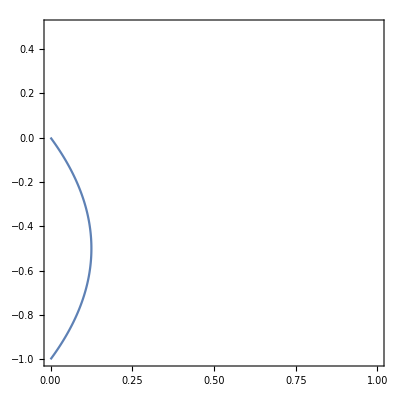

```mathematica
ContourPlot[{λ^2+λ+2v==0},{v,0,1},{λ,-1,.5},PlotPoints->200]
```

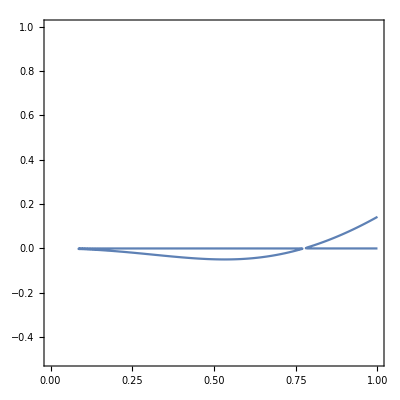

```mathematica
ContourPlot[{λ+v/Γ d2==0},{v,0,1},{λ,-.5,1},PlotPoints->200]
```